```mathematica
import=filename↦Import[NotebookDirectory[]<>"/data-source/csse_covid_19_data/csse_covid_19_time_series/"<>filename];
confirmed=import["time_series_19-covid-Confirmed.csv"];
dead=import["time_series_19-covid-Deaths.csv"];
recovered=import["time_series_19-covid-Recovered.csv"];
stripNonValues=#[[5;;]]&;
header=confirmed[[1]];
parseShittyDate=fuckoff↦DateObject[
Map[
ToExpression,
Part[StringSplit[fuckoff,"/"],{3,1,2}]
]/.{y_,m_,d_}->{y+2000,m,d}
];
daysSince2020=Map[Composition[(#-UnixTime[{2020,1,1}])/(60 60 24)&,UnixTime,parseShittyDate],stripNonValues[header]];
onlyGerman=data↦Select[data,#[[2]]=="Germany"&][[1]];
germanConfirmed=stripNonValues[onlyGerman[confirmed]];
germanDead=stripNonValues[onlyGerman[dead]];
germanRecovered=stripNonValues[onlyGerman[recovered]];

timeSeries=data↦Transpose[{daysSince2020,data}];
dayOffsetToTick=offset↦DateString[DatePlus[DateObject["2020-01-01"],offset],{"MonthNameShort", " ","Day"}];
ticksWeekly={Table[{day,dayOffsetToTick[day]},{day,5,100,7}],Automatic};
```

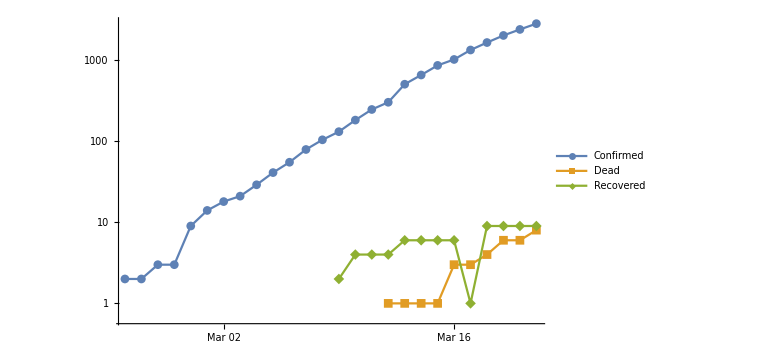

```mathematica
ListLogPlot[
timeSeries/@{germanConfirmed,germanDead,germanRecovered},
Joined->True,
PlotMarkers->Automatic,
PlotLegends->{"Confirmed","Dead","Recovered"},
ImageSize->Large,
Ticks->ticksWeekly
]
```

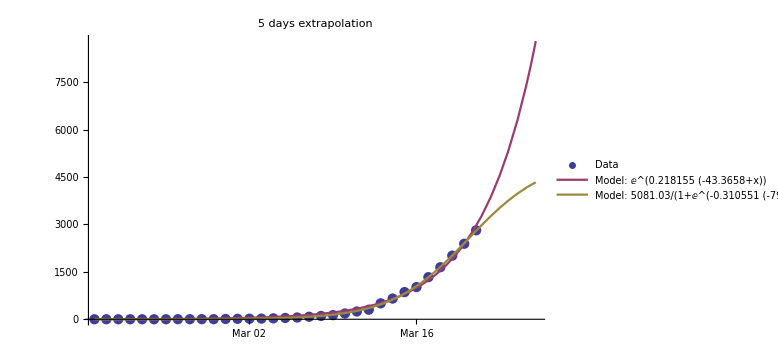
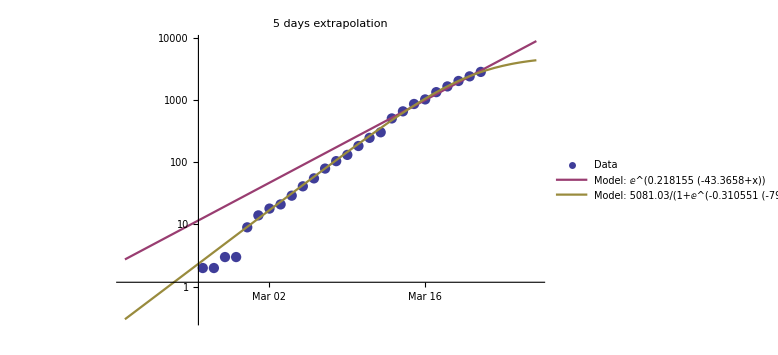
Doubling every 3.2 days
 | Estimate | Standard Error | t-Statistic | P-Value
a | 0.218155 | 0.00532749 | 40.9489 | 1.47838×10^-28
x0 | 43.3658 | 0.851799 | 50.9109 | 1.90604×10^-31
 | Estimate | Standard Error | t-Statistic | P-Value
a | 5081.03 | 211.248 | 24.0525 | 3.65354×10^-21
β | 3.22009 | 0.0639528 | 50.351 | 1.52086×10^-30
x0 | 79.3442 | 0.260397 | 304.705 | 6.28311×10^-54
-Graphics-
-Graphics-

```mathematica
logExtrapolation={dataInput,startDayString,daysToExtrapolate}↦Module[
{data=dataInput},

startDay=DateValue[startDayString,"ISOYearDay"];

data=Select[data,#/.{t_,_}->t≥startDay&];
expFit=NonlinearModelFit[data,Exp[a (x-x0)],{{a,0.3},{x0,40}},x];
logisticFit=NonlinearModelFit[data,a*CDF[LogisticDistribution[x0,β],x],{{a,60000},{β,3},{x0,80}},x];
timeCoordinates=Map[#/.{t_,_}->t&,data];
{from,to}={Min[timeCoordinates],Max[timeCoordinates]};

mmaColors=ColorData[1,"ColorList"];
dataPlot=ListPlot[data,PlotRange->All,PlotStyle->mmaColors[[1]],PlotLegends->{"Data"},Ticks->ticksWeekly];
expModelPlot=Plot[expFit[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[2]],PlotLegends->{Row@{"Model: ",Normal[expFit]}},Ticks->ticksWeekly];
logisticModelPlot=Plot[logisticFit[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[3]],PlotLegends->{Row@{"Model: ",Normal[logisticFit]}},Ticks->ticksWeekly];

dataLogPlot=ListLogPlot[data,PlotRange->All,PlotStyle->mmaColors[[1]],PlotLegends->{"Data"},Ticks->ticksWeekly];
expModelLogPlot=LogPlot[expFit[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[2]],PlotLegends->{Row@{"Model: ",Normal[expFit]}},Ticks->ticksWeekly];
logisticModelLogPlot=LogPlot[logisticFit[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[3]],PlotLegends->{Row@{"Model: ",Normal[logisticFit]}},Ticks->ticksWeekly];

combinedShow={d,m,l}↦Show[d, m,l,ImageSize->Large,PlotRange->All,PlotLabel->ToString[daysToExtrapolate]<>" days extrapolation"];
{
expFit,
"Doubling every "<>ToString[Round[Log[2]/(a/.expFit["BestFitParameters"]),0.1]]<>" days",
expFit["ParameterTable"],
logisticFit["ParameterTable"],
combinedShow[dataPlot, expModelPlot,logisticModelPlot],
combinedShow[dataLogPlot, expModelLogPlot,logisticModelLogPlot]
}
];
result=logExtrapolation[timeSeries[germanConfirmed],"2020-02-17",5];
result/.{_,rest__}->Column[List[rest]]
```